# Simple Task 11

Brian Carlson

### Task

(i) Find two quantities in the CountryData database that you want to relate to each other.
and produce a scatter plot of the data.
(ii) Describe the relationship you are seeing and why you believe it occurs.
(iii) Choose an appropriate best fit function for your data and show a plot with the best fit function.
Justify the choice of the best fit function with a sentence.
Compute the RSquared value and write a sentence commenting on the quality of the fit.

### Solution to Part I

```mathematica
points=Select[{CountryData[#,"GDP"]/CountryData[#,"Population"],CountryData[#,"GovernmentConsumption"]/CountryData[#,"Population"]}&/@CountryData[],NumberQ[#[[2]]]&];
```

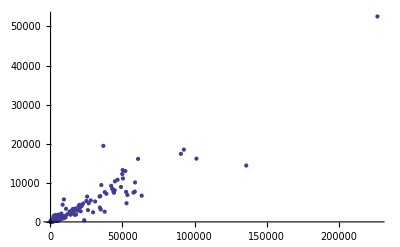

```mathematica
ListPlot[Tooltip[{CountryData[#,"GDP"]/CountryData[#,"Population"],CountryData[#,"GovernmentConsumption"]/CountryData[#,"Population"]},CountryData[#,"Name"]]&/@CountryData[],PlotRange->All]
```

### Solution to Part II

Since the GDP is a measure of the gross domestic product, dividing it by population would give the GDP per person, similar to wealth per person. It would make sense that the government consumption per person would increase as the wealth per person increases because a country with a higher GDP per person would have more taxable income at its disposal to spend per person.

### Solution to Part III

```mathematica
equ=NonlinearModelFit[points,a*x+b,{a,b},x]
```

FittedModel[-104.142+0.191161 x]

Government consumption should be linearly dependent on the GDP per person.

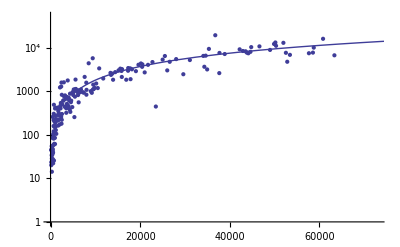
-Graphics-Log_10[Government Consumption per person]GDP per person

```mathematica
Labeled[Show[{ListLogPlot[points],LogPlot[equ[x],{x,Min[#[[1]]&/@points],Max[#[[1]]&/@points]}]}],{"Log_10[Government Consumption per person]","GDP per person"},{Left,Bottom},RotateLabel->True]
```

```mathematica
equ["RSquared"]
```

0.905021

The R-Squared value indicates that this is a good fit.